Entanglement and Entropy

Quantum Entanglementpaclet:QuantumMob/Q3/tutorial/EntanglementAndEntropy#1806116627 | Entanglement Distillationpaclet:QuantumMob/Q3/tutorial/EntanglementAndEntropy#2030356719
Separability Testspaclet:QuantumMob/Q3/tutorial/EntanglementAndEntropy#16197061 | Entanglement Measurespaclet:QuantumMob/Q3/tutorial/EntanglementAndEntropy#1685747456

Interacting systems, classical or quantum, tend to build correlation among them. Entanglement is a type of correlation. However, it exhibits many interesting correlation effects that are specifically quantum and cannot be simulated classically. Many protocols for quantum information processing, quantum communication, and quantum cryptography utilize entanglement as the key resource.
In this article, we discuss how to characterize, manipulate, and quantify entanglement. The subjects pose many open questions and are currently under active research. Therefore, our discussion will remain at the elementary and introductory level. Motivated readers are referred to Horodecki et al. (2009)https://doi.org/10.1103/RevModPhys.81.865.

VonNeumannEntropypaclet:QuantumMob/Q3/ref/VonNeumannEntropyQuantumMob Package Symbol | The von Neumann entropy of a mixed state
PartialTracepaclet:QuantumMob/Q3/ref/PartialTraceQuantumMob Package Symbol | The partial trace of the quantum state of a larger system
LogarithmicNegativitypaclet:QuantumMob/Q3/ref/LogarithmicNegativityQuantumMob Package Symbol | The logarithmic negativity as an entanglement measure
Negativitypaclet:QuantumMob/Q3/ref/NegativityQuantumMob Package Symbol | The negativity as an entanglement measure

Q3 functions related to quantum entanglement.

Make sure that the Q3: Symbolic Quantum Simulation package is loaded to use the demonstrations in this documentation.

```mathematica
Needs["QuantumMob`Q3`"]
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
```

Quantum Entanglement

We consider a composite system AB consisting of two subsystems A and B. The two systems are associated with the Hilbert space 𝒱 and 𝒲, respectively. We suppose that {v_i} and {w_j} are orthonormal bases of 𝒱 and 𝒲, respectively. We often use the shorthand notation v_i w_j≡v_i⊗w_j for the tensor-product basis states. Entanglement across more than two parties is also an important subject, but here we will only discuss bipartite case.

Suppose that Ψ_AB is a pure state of the composite system. Ψ_AB is a separable state if it can be written in a product form

Ψ_AB=α_A⊗β_B .

Otherwise, it is an entangled state.

As for mixed states, the separability allows not only product states but also any convex linear combination of product states. In other words, a mixed state ρ_AB of the composite system is said to be separable if it can be written in the form

ρ_AB=Σ_j p_j ρ_j⊗σ_j ,

where ρ_j and σ_j are density operators on A and B, respectively, and 0≤p_j≤1 and Σ_j p_j=1. If not, ρ_AB is said to be entangled.

Separability Tests

Given a quantum state, how can we tell if it is separable or entangled? For pure states, the Schmidt decomposition provides a straightforward method. See Appendix A.6.1 of the Quantum Workbook for details.

For a mixed state, there is no simple method available to check if it is separable or entangled. Here, we introduce a few well-known methods.

A powerful method is to use the partial transposition (Appendix B.4 of the Quantum Workbook). It was discovered by Peres (1996) and has inspired many other methods for separability tests of mixed states. Let L be a linear operator on the composite system consisting of subsystems A and B. In the standard tensor-product basis, the partial transposition of L with respect to B is defined by the relation

v_i w_j L^T_B v_k w_l=v_i w_lLv_k w_j .

The partial transposition L^T_A of L with respect to A is defined analogously.

The so-called positive partial transposition criterion states that if ρ_AB is separable, then the partial transposition ρ_AB^T_B of ρ is positive. As an example, consider a Werner state,

ρ_AB=1/4 I⊗I-p/4(X⊗X+Y⊗Y+Z⊗Z) .

The partial transposition of it with respect to B is given by

ρ_AB^T_B=1/4 I⊗I^T-p/4(X⊗X^T+Y⊗Y^T+Z⊗Z^T)=1/4 I⊗I-p/4(X⊗X-Y⊗Y+Z⊗Z) .

A direct inspection of the eigenvalues of ρ_AB^T_B reveals that for p>1/3, two of the eigenvalues become negative. The positive partial transposition criterion is violated and the state must be an entangled state.

```mathematica
Needs["QuantumMob`Q3`"]
```

```mathematica
Let[Qubit,S]
```

We consider a Werner state, and apply the positive partial transposition criterion.

We first prepare two qubits in the singlet state.

```mathematica
singlet=(Ket[S[2]->1]-Ket[S[1]->1])/Sqrt[2]//KetRegulate
```

(0_(,,S_(,,1))1_(,,S_(,,2))-1_(,,S_(,,1))0_(,,S_(,,2)))/(√2)

A Werner state is a convex linear superposition of the single state and the completely random mixture.

```mathematica
rho=p*Dyad[singlet,singlet,S@{1,2}]+(1-p)/4//Elaborate
rho//Matrix//MatrixForm
```

1/4-1/4 p S_(,,1)^(,,X)S_(,,2)^(,,X)-1/4 p S_(,,1)^(,,Y)S_(,,2)^(,,Y)-1/4 p S_(,,1)^(,,Z)S_(,,2)^(,,Z)

(1/4-p/4 | 0 | 0 | 0
0 | 1/4+p/4 | -p/2 | 0
0 | -p/2 | 1/4+p/4 | 0
0 | 0 | 0 | 1/4-p/4)

This is the partial transposition of rho with respect to the second qubit.

```mathematica
new=PartialTranspose[rho,S[2]]//Elaborate
new//Matrix//MatrixForm
```

1/4-1/4 p S_(,,1)^(,,X)S_(,,2)^(,,X)+1/4 p S_(,,1)^(,,Y)S_(,,2)^(,,Y)-1/4 p S_(,,1)^(,,Z)S_(,,2)^(,,Z)

(1/4-p/4 | 0 | 0 | -p/2
0 | 1/4+p/4 | 0 | 0
0 | 0 | 1/4+p/4 | 0
-p/2 | 0 | 0 | 1/4-p/4)

This shows the eigenvalues of the partial transposition of rho. For p<1/3, all eigenvalues are positive and the positive partial transposition is satisfied. However, two of the eigenvalues get negative for p>1/3, and hence the state must be entangled.

```mathematica
Plot[Evaluate@ProperValues[new],{p,0,1},FrameLabel->{"p","Eigenvalues"},PlotLegends->Automatic]
```

-Graphics-

We apply the positive partial transposition criterion to another example. Again, we first prepare two qubits in the singlet state.

```mathematica
singlet=(Ket[S[2]->1]-Ket[S[1]->1])/Sqrt[2]//KetRegulate
```

(0_(,,S_(,,1))1_(,,S_(,,2))-1_(,,S_(,,1))0_(,,S_(,,2)))/(√2)

The state we are concerned with is a mixture of the singlet state and a fully polarized state, pSS+(1-p)0000.

```mathematica
rho=p*Dyad[singlet,singlet,S@{1,2}]+(1-p)Dyad[Ket[],Ket[],S@{1,2}]//Elaborate
rho//Matrix//Simplify//MatrixForm
```

1/4-1/4 p S_(,,1)^(,,X)S_(,,2)^(,,X)-1/4 p S_(,,1)^(,,Y)S_(,,2)^(,,Y)+1/4 (1-2 p) S_(,,1)^(,,Z)S_(,,2)^(,,Z)+1/4 (1-p) S_(,,1)^(,,Z)+1/4 (1-p) S_(,,2)^(,,Z)

(1-p | 0 | 0 | 0
0 | p/2 | -p/2 | 0
0 | -p/2 | p/2 | 0
0 | 0 | 0 | 0)

This is the partial transposition of rho with respect to the second qubit.

```mathematica
new=PartialTranspose[rho,S[2]]//Elaborate
new//Matrix//Simplify//MatrixForm
```

1/4-1/4 p S_(,,1)^(,,X)S_(,,2)^(,,X)+1/4 p S_(,,1)^(,,Y)S_(,,2)^(,,Y)+1/4 (1-2 p) S_(,,1)^(,,Z)S_(,,2)^(,,Z)+1/4 (1-p) S_(,,1)^(,,Z)+1/4 (1-p) S_(,,2)^(,,Z)

(1-p | 0 | 0 | -p/2
0 | p/2 | 0 | 0
0 | 0 | p/2 | 0
-p/2 | 0 | 0 | 0)

This shows that for all 0<p≤1, the partial transposition has a negative eigenvalue. Therefore, the state must be entangled.

```mathematica
Plot[Evaluate@ProperValues[new],{p,0,1},FrameLabel->{"p","Eigenvalues"},PlotLegends->Automatic]
```

-Graphics-

Unfortunately, the positive partial transposition is a necessary but not sufficient condition for separability. Nevertheless, it is a very strong condition and gives a good guide for separability of the quantum state in question. Moreover, it is a necessary and sufficient condition in the 2⊗2 and 2⊗3 cases, that is, when dimV=2 and dimW=2,3.

Later, people realized that it was not by chance that the positive partial transposition criterion gives a strong necessary condition for separability. The crucial point is that the transposition, regarded as a supermap, is positive but not completely positive (Appendix B.4 of the Quantum Workbook). Let ℱ be the transposition supermap, ℱ:A→ A^T . Then, the partial transposition corresponds to ℐ⊗ ℱ (or ℱ⊗ℐ). It turns out that any positive but not completely positive supermap ℱ gives rise to a necessary condition for separability. If ρ_AB is separable, then (ℐ⊗ ℱ)(ρ_AB) must be positive.

We now introduce the method based on entanglement witness. An observable W is called an entanglement witness if it has at least one negative eigenvalue and satisfies

(α⊗β)W(α⊗β)≥0

for all pure states α and β of A and B, respectively. A quantum state ρ_AB is a separable state if

Tr[W ρ_AB]≥0

for all entanglement witnesses. On the other hand, the entanglement of ρ_AB is detected by an entanglement witness W if and only if Tr[W ρ_AB]<0. This method works for a geometrical reason. The set of separable states is a convex subset in the entire Hilbert space 𝒱⊗𝒲 and can be described by hyperplanes. An entanglement witness represents a hyperplane.

Entanglement Distillation

Suppose that Alice and Bob share a pair of entangled but not maximally entangled state. By now they are separated far way and no quantum channel is available. Luckily, they can still communicate through a classical channel. Is it possible for them to transform their partially entangled state to a maximally entangled state? The answer is no. Local operations and classical communications (often called LOCC) cannot generate or increase entanglement.

Now, suppose that they have a large number n of copies of a partially entangled state Ψ. Although they cannot transform each pair to a maximally entangled state, they can extract a smaller number k (k<n) of maximally entangled pairs. This is called the entanglement distillation. The entanglement distillation is not only useful for practical applications but also valuable for a fundamental reason. It can quantify entanglement. We will come back to this point later.

So, how can Alice and Bob extract maximally entangled pairs from partially entangled pairs using only local operations and classical communications? For an illustration, we follow Preskill (1998) and suppose that the state of each partially entangled pair is

Ψ=0⊗0 √(1-p)+1⊗1 √p .

The overall state of the n pairs is given by

Ψ^(⊗n)=(0⊗0 √(1-p)+1⊗1 √p)^(⊗n) .

The binomial expansion of the right-hand side of the above expression leads to

Ψ^(⊗n)=Σ_(m=0)^n(Ψ_m(n
m))^(1/2)(1-p)^((n-m)/2)p^(m/2) ,

where Ψ_m is an entangled state of the form

Ψ_m:=(n
m)^(-1/2)(00…⊗00…+01…⊗01…+…)

with Schmidt rank R=(n
m), and each term has exactly m of Alice’s (and Bob’s) qubits in state 1. Now, Alice measures the total spin of her n qubits along the z-axis

S_total^z:=Σ_(j=1)^n S_j^z .

The possible outcomes are m=0,1,…,n. For each outcome m, the post-measurement state is nothing but Ψ_m. The probability for a particular outcome m is given by

P_m=(n
m)(1-p)^(n-m)p^m .

As illustrated in Figure 1, P_m has a sharp peak at m=np for large n. Therefore, from now on, we will assume that m=np.

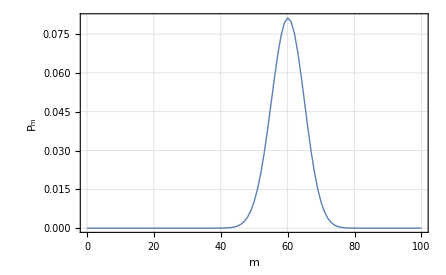

Figure 1. The probability P_m for outcome m from the measurement of the total spin along the z-axis, S_total^z:=∑_(j=1)^n S_j^z, on Alice’s qubits. The plot is for n=100 and p=3/5.

Next, Alice and Bob are to convert Ψ_m to independent copies of maximally entangled pairs.Suppose that R≈(n
np) = 2^k for some integer k≤n. Then, recalling that

1/2^(n/2)Σ_(x=0)^(2^n-1)x⊗x=1/2^(n/2)⊗_(j=1)^n(0_j⊗0_(n+j)+1_j⊗1_(n+j)) ,

it is possible to transform the state to k copies of maximally entangled pairs. To do that, both Alice and Bob perform a transformation bringing the 2^k-dimensional support of her and his respective density operators to the Hilbert space of k qubits.

Here, we start with a number of partially entangled pairs and “distills” a smaller number of maximally entangled pairs.

We have two parties Alice (A) and Bob (B). Teddy (T)  is an ancillary register to perform a measurement of the total Pauli Z.

```mathematica
Needs["QuantumMob`Q3`"]
```

```mathematica
Let[Qubit,A,B,T]
```

We will start with n partially entangled pairs.

```mathematica
$n=4;
kk=Range[$n];
AA=A[kk,$];
BB=B[kk,$];
```

You need fewer qubits for T, just enough to store a number up to maximum n.

```mathematica
ln=Ceiling@Log[2,$n+1];
TT=T[Range@ln,$];
```

Let us first examine a single pair of partially entangled qubits.  First, construct a superposition of the two computational basis states with different amplitudes.

```mathematica
Let[Real,ϕ]
qc=QuantumCircuit[
Ket[A@{1}],
Rotation[ϕ,A[1,2]]]
```

-Graphics-

Parameter ϕ tunes the two amplitudes, c_0=cos(ϕ/2) and c_1=sin(ϕ/2), in the superposition.

```mathematica
Elaborate[qc]//ExpandAll
```

Cos[ϕ/2] 0_(,,A_(,,1))+1_(,,A_(,,1)) Sin[ϕ/2]

Then, by applying the CNOT gate, you can create a partially entangled pair.

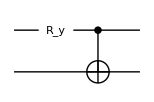

```mathematica
qc=QuantumCircuit[
Ket[{A[1],B[1]}],
Rotation[ϕ,A[1,2]],
CNOT[A[1],B[1]]]
```

Eventually, we see that the parameter ϕ tunes the extent of entanglement  (with ϕ=π/2 corresponds to the maximal entanglement).

```mathematica
out=Elaborate[qc]
```

Cos[ϕ/2] 0_(,,A_(,,1))0_(,,B_(,,1))+1_(,,A_(,,1))1_(,,B_(,,1)) Sin[ϕ/2]

Examine the reduced density matrix for the first qubit to check that the above state is partial entangled.

```mathematica
rho=PartialTrace[out,B[1]]//ExpToTrig//Simplify;
Matrix[rho]//ExpToTrig//SimplifyThrough//MatrixForm
```

(Cos[ϕ/2]^2 | 0
0 | Sin[ϕ/2]^2)

Now, we consider n partially entangled pairs with each pair in the state described above. Let us take a look at the explicit expression for the n partially entangled pairs. Repeating the above procedure for other pairs, generate as many partially entangled pairs as  you like. In this particular example, we prepare four pairs.

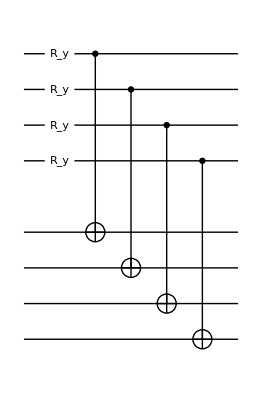

```mathematica
qc0=QuantumCircuit[
Ket[AA],Ket[BB],
Rotation[ϕ,A[kk,2]],
Sequence@@ReleaseHold@Thread@Hold[CNOT][AA,BB],
"Invisible"->A[$n+1/2]
]
```

Expanding it, one gets various terms, each with identical parts on Alice’s and Bob’s side.

```mathematica
out=Elaborate[qc0];
ProductForm[out,{AA,BB}]
```

Cos[ϕ/2]^4 ⊗⊗00000000+Cos[ϕ/2]^3 ⊗⊗00010001 Sin[ϕ/2]+⊗⊗11111111 Sin[ϕ/2]^4+1/2 Cos[ϕ/2]^2 ⊗⊗01000100 Sin[ϕ]+1/2 Cos[ϕ/2]^2 ⊗⊗10001000 Sin[ϕ]+1/2 ⊗⊗01110111 Sin[ϕ/2]^2 Sin[ϕ]+1/2 ⊗⊗10111011 Sin[ϕ/2]^2 Sin[ϕ]+1/2 ⊗⊗11011101 Sin[ϕ/2]^2 Sin[ϕ]+1/2 ⊗⊗11101110 Sin[ϕ/2]^2 Sin[ϕ]+1/4 Cot[ϕ/2] ⊗⊗00100010 Sin[ϕ]^2+1/4 ⊗⊗00110011 Sin[ϕ]^2+1/4 ⊗⊗01010101 Sin[ϕ]^2+1/4 ⊗⊗01100110 Sin[ϕ]^2+1/4 ⊗⊗10011001 Sin[ϕ]^2+1/4 ⊗⊗10101010 Sin[ϕ]^2+1/4 ⊗⊗11001100 Sin[ϕ]^2

If Alice (or Bob) measures the total Z, i.e., Z=Z_1+Z_2+…+Z_n on her qubits (see below), then the possible outcomes are  m=0,1,…,n and the corresponding probabilities are given by the following formula.

```mathematica
Clear[prb]
prb[ϕ_,m_]:=With[{p=Sin[ϕ/2]^2},Binomial[$n,m]*(1-p)^($n-m)p^m]
prb[ϕ,m]//Simplify
```

Binomial[4,m] (Cos[ϕ/2]^2)^(4-m) (Sin[ϕ/2]^2)^m

For fixed ϕ, the probability distribution looks like the following plot. The highest probability is for m=nsin^2(ϕ/2) (m=3 for ϕ=2π/3).

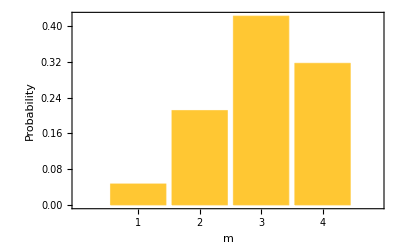

```mathematica
BarChart[
Table[prb[2Pi/3,m],{m,$n}],
ChartLabels->Range[$n],
Axes->None,Frame->True,
FrameLabel->{"m","Probability"}
]
```

How can we actually measure Z_tot:=Z_1+Z_2+…+Z_non Bob's (or, equivalently, Alice's) qubits?

To specific, we assume ϕ=2π/3 from now on.

```mathematica
ϕ=2Pi/3
```

(2 π)/3

This is a tiny utility function for convenience.

```mathematica
bundle[]:=Flatten@Table[bundle[c],{c,$n}]
bundle[c_]:=With[
{log=Ceiling@Log[2,c+1]},
Table[
CNOT[Prepend[T@Range[k-1],B[c]],T[k]],
{k,log,1,-1}
]
]
```

The value of Z_tot is stored on Teddy's register.

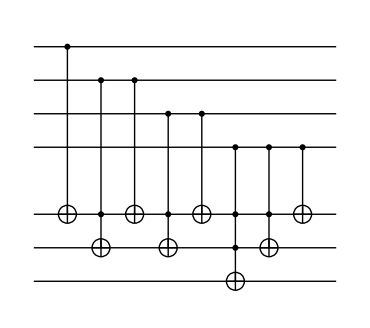

```mathematica
qc1=QuantumCircuit[
Ket[TT],
Sequence@@bundle[],
"Invisible"->B[$n+1/2]]
```

Let us check that the above quantum circuit indeed gives the sum of the bit values of the Bob’s qubits.

```mathematica
in=Basis[BB];
out=qc1**in;
```

```mathematica
sum=FromDigits[#,2]&/@Reverse/@Through[out[TT]];
Thread[SimpleForm[in]->sum]//TableForm
```

;;0000→0
;;0001→1
;;0010→1
;;0011→2
;;0100→1
;;0101→2
;;0110→2
;;0111→3
;;1000→1
;;1001→2
;;1010→2
;;1011→3
;;1100→2
;;1101→3
;;1110→3
;;1111→4

In actual situation, one must perform the measurement on Teddy's register in the computational basis. The measurement outcome refers to the value of Z_tot.

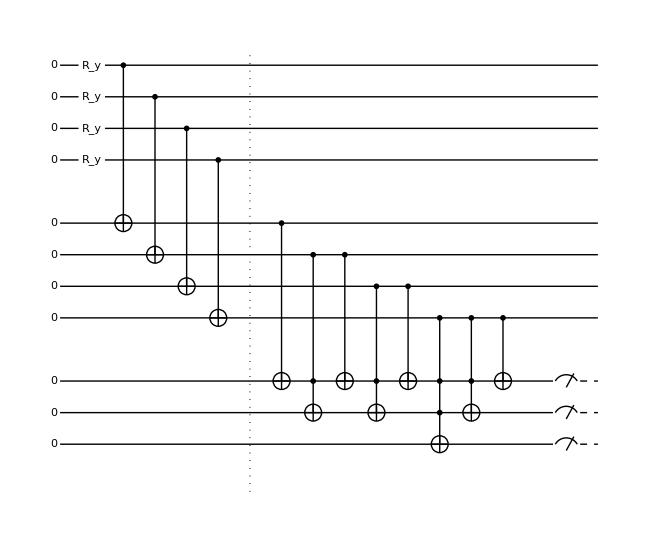

```mathematica
qc2=QuantumCircuit[
"Invisible"->{A[$n+1/2],B[$n+1/2],T[5]},
qc0,"Separator",qc1,"Spacer",Measurement[T[Range@ln,3]]]
```

The post-measurement state is spread over the four qubits of Alice's and Bob's registers, respectively. One has to transform it into a smaller number of pairs. Here, we assume that the measurement outcome is Z_tot=3, corresponding to two maximally entangled pairs. Note that  measurement outcome Z_tot=1also leads to two maximally entangled pairs since Binomialpaclet:ref/Binomial[4,1]==Binomialpaclet:ref/Binomial[4,3]==4.

To get the unitary transformation on Alice's side, we first rearrange the computational basis to get a new basis

𝒜:={0111,1011,1101,1110,α_5,…,α_16},

where α_k (k=5,…,16) are the computational basis states with total spin not equal to 3. Next, consider still another basis
	𝒜':={00;00,01;00,10;00,11;00,α'_5,…,α'_16},

where we have put a semicolon ';' to indicate the first two qubits to which encode Alice’s part of the maximally entangled states. Then, the required unitary transformation corresponds to the basis change from 𝒜 to 𝒜'. That is to say, the unitary transformation is given by

U:=00;000111+01;001011+10;001101+11;001110+Σ_(k=5)^16 a'_kα_k.

The unitary transformation on Bob's register may be obtained in the same manner, where we denote the rearranged bases by ℬ and ℬ'

These are the computational bases for Alice's and Bob's registers, respectively.

```mathematica
bsA=Basis[AA]
bsB=Basis[BB]
```

{0_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),0_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4))}

{0_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),0_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4))}

These are the bases 𝒜 and ℬ for Alice's and Bob's registers, respectively.

```mathematica
bb=Permutations[PadLeft[Table[1,3],$n]];
sppA=Ket[AA->#]&/@bb;
sppB=Ket[BB->#]&/@bb;
sppA=Join[sppA,Sort@Complement[bsA,sppA]]
sppB=Join[sppB,Sort@Complement[bsB,sppB]]
```

{0_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),0_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4))}

{0_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),0_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4))}

These are the bases 𝒜' and ℬ' for Alice's and Bob's registers, respectively.

```mathematica
newA=Basis[A@{1,2}]//KetRegulate[#,AA]&;
newB=Basis[B@{1,2}]//KetRegulate[#,BB]&;
newA=Join[newA,Sort@Complement[bsA,newA]]
newB=Join[newB,Sort@Complement[bsB,newB]]
```

{0_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),0_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),0_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))0_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))1_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))0_(,,A_(,,4)),1_(,,A_(,,1))1_(,,A_(,,2))1_(,,A_(,,3))1_(,,A_(,,4))}

{0_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),0_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),0_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))0_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))1_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))0_(,,B_(,,4)),1_(,,B_(,,1))1_(,,B_(,,2))1_(,,B_(,,3))1_(,,B_(,,4))}

Then, the unitary transformation is constructed as prescribed above.

```mathematica
trsA=Total@MapThread[Dyad[#1,#2,AA]&,{newA,sppA}]
trsB=Total@MapThread[Dyad[#1,#2,BB]&,{newB,sppB}]
```

-Graphics-

-Graphics-

Now, we have all components. Our desired quantum circuit is as follows. The first part generates four partially entangled pairs, the second measures the total Pauli Z on Bob's register, and the last transforms the post-measurement state a fixed pair of qubits from Alice's and Bob's registers.

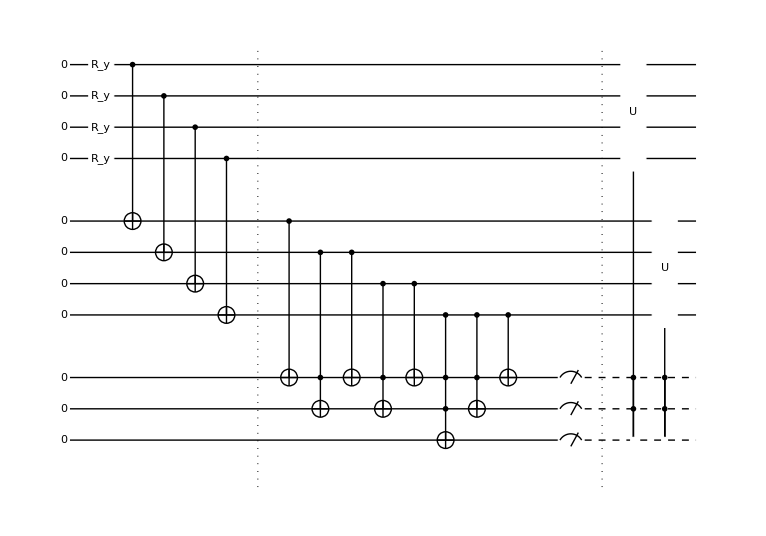

```mathematica
all=QuantumCircuit[qc2,"Separator",
ControlledGate[T@{1,2,3}->{1,1,0},trsA,"Label"->"U"],
ControlledGate[T@{1,2,3}->{1,1,0},trsB,"Label"->"U"],
]
```

Because the transformation on Alice’s and Bob’s sides are designed for the measurement outcome of Z_tot=3, we just run the quantum circuit until we get the desired outcome.

```mathematica
Until[ztot==3,
out=Elaborate[all];
ztot=FromDigits[Reverse@Readout[Through[TT[3]]],2];
PrintTemporary["Z_tot=",ztot]
];
```

Here is the output state of the total system. Obviously, the whole register T is separated from the other two registers. So are the last two registers of the respective registers A and B.

```mathematica
out
```

1/2 0_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4))0_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4))1_(,,T_(,,1))1_(,,T_(,,2))0_(,,T_(,,3))+1/2 0_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4))0_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4))1_(,,T_(,,1))1_(,,T_(,,2))0_(,,T_(,,3))+1/2 1_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4))1_(,,B_(,,1))0_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4))1_(,,T_(,,1))1_(,,T_(,,2))0_(,,T_(,,3))+1/2 1_(,,A_(,,1))1_(,,A_(,,2))0_(,,A_(,,3))0_(,,A_(,,4))1_(,,B_(,,1))1_(,,B_(,,2))0_(,,B_(,,3))0_(,,B_(,,4))1_(,,T_(,,1))1_(,,T_(,,2))0_(,,T_(,,3))

Focusing on the first two qubits of registers A and B, we see that there are two maximally entangled pairs.

```mathematica
SimpleForm[out,{A@{1,2},B@{1,2}}]
```

1/2 ;;0000+1/2 ;;0101+1/2 ;;1010+1/2 ;;1111

```mathematica
KetFactor@KetDrop[out,TT]
```

1/2 0_(,,A_(,,3))0_(,,A_(,,4))⊗(0_(,,A_(,,1))0_(,,B_(,,1))+1_(,,A_(,,1))1_(,,B_(,,1)))⊗(0_(,,A_(,,2))0_(,,B_(,,2))+1_(,,A_(,,2))1_(,,B_(,,2)))⊗0_(,,B_(,,3))0_(,,B_(,,4))

Remark: So, we have successfully generated two maximally entangled pairs from four partially entangled pairs. Note that this was possible because we assumed that the measurement outcome was m=3. The case with m=1 is also handled following a similar procedure.

However, if the measurement outcome is m=2, resulting in the post-measurement state

1/6 0011⊗0011+1/6 0101⊗0101+1/6 0110⊗0110+1/6 1001⊗1001+1/6 1010⊗1010+1/6 1100⊗1100

then there is no way to turn this state into a product state on a system of qubits.

In general, R is not close to a power of 2. However, one can increase the chance by dividing the entire pairs into l blocks of n pairs. Alice perform the previously prescribed measurement on each block. Then, the total Schmidt rank becomes

R≈(n
m_1)(n
m_2)…(n
m_l)

with m_j≈np for every j. For some l, R now approaches 2^k.

How many maximally entangled pairs can one extract from nl partially entangled pairs? Recall that for large n,

(n
m)≈2^(nH(m/n)) ,

where

H(p):=H({p,1-p})=-plogp-(1-p)log(1-p)

is the binary entropy function. Then, we have

R≈2^(nH(p))≈2^k,

which implies that the ratio is governed by the von Neumann entropy

k/nl=H(p)=S(ρ_A) .

In the above demonstration, we have used a particular form of partially entangled state. However, the result holds true in general: Given n copies of partially entangled pure state Ψ_AB, one can extract at most k_max=nS(ρ_A) maximally entangled pairs. The ratio k_max/n in the large n limit thus characterizes to what extent the state Ψ_AB is entangled. Clearly, for pure state, it happens to be given by the von Neumann entropy. In the subsection, we will see that this is a good measure of entanglement for mixed states as well.

Entanglement Measures

For both operational purposes and fundamental reasons, it is desired to quantify entanglement in a quantum state. For a pure state Ψ_AB, the Schmidt decomposition

Ψ_AB=Σ_j α_j⊗β_j s_j

is a good starting point. We see that the more uniformly the Schmidt values {s_j} are distributed, the more extensive the entanglement is. Therefore, it is reasonable to quantify the entanglement of Ψ_AB by the Shannon entropy H({s_j}) associated with the distribution {s_j}. Since it is identical to the von Neumann entropy of subsystems,

S(ρ_A)=S(ρ_B)=H({s_j}) ,

we define the entanglement measure by

E:=S(ρ_A)=S(ρ_B) .

It is called the entropy of entanglement or simply entanglement entropy. In the previous section, we have seen that S(ρ_A) also determines the entanglement distillation ratio for pure states. The initial idea to quantify entanglement was elevated by the view of entanglement as a resource for quantum communication. Since a maximally entangled state can quantum teleport one qubit, it is natural to compare the given state with the maximally entangled state. Many entanglement measures are based on this idea. The most common examples are the distillable entanglement and entanglement cost.

The distillable entanglement arises in the situation that we have already encountered in the previous section. There, we have considered only pure states. Now, consider a partially entangled mixed state ρ_AB. Suppose that Alice (A) and Bob (B) share n copies of pairs with each in ρ_AB. We ask what is the maximum number k_max of maximally entangled pairs that can be extracted from the partially entangled pairs. The distillable entanglement is defined by the ratio,

E_D:=k_max/n

in the large n limit.

The entanglement cost arises in the opposite situation. Suppose that Alice and Bob share k maximally entangled pairs. Alice and Bob want to generate n pairs with each in a given state ρ_AB. We ask what is the minimum value k_min of k? We define the entanglement cost by

E_C:=k_min/n

in the large n limit.

For pure states, both are identical to the entropy of entanglement,

E_D=E_C=E=S(ρ_A)=S(ρ_B) .

Unfortunately, for mixed state, both E_D and E_C are usually very difficult to
calculate.

Another noteworthy entanglement measure is the logarithmic negativity. It is inspired by the positive partial transposition criterion in the “Separability Tests” section, and defined by

E_N:=log(‖ρ_AB^T_B‖)_tr

where ∥·∥_tr denotes the trace norm. Unlike other entanglement measures for mixed states, the logarithmic negativity is easy to evaluate. However, it does not reduce to the entropy of entanglement for all pure states.

```mathematica
Needs["QuantumMob`Q3`"]
```

```mathematica
Let[Qubit,S]
```

The entanglement measures for mixed states enable to investigate multi-partite entanglement. As an example, we consider the control and target registers each of which is consisting of n qubits and use the logarithmic negativity to characterize the multi-partite entanglement in the system.

```mathematica
$n=2;
cc=Range[$n];
tt=$n+cc;
```

We generate a quantum state with a maximally entanglement between the control and target registers.

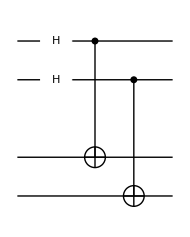

```mathematica
qc=QuantumCircuit[S[cc,6],
Sequence@@MapThread[CNOT,{S[cc],S[tt]}],
"Invisible"->S[$n+1/2]]
```

This is the desired state.

```mathematica
out=qc**Ket[]
```

1/2 0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))+1/2 0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))+1/2 1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))+1/2 1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))

Note that even through the state exhibits a maximal entanglement between the control and target registers, it is product state between two registers respectively containing qubits 1 and 3 and qubits 2 and 4.

```mathematica
KetFactor[out]
```

1/2 (0_(,,S_(,,1))0_(,,S_(,,3))+1_(,,S_(,,1))1_(,,S_(,,3)))⊗(0_(,,S_(,,2))0_(,,S_(,,4))+1_(,,S_(,,2))1_(,,S_(,,4)))

Keeping in mind the above fact, we examine a mixed state of the control register that has been obtained by tracing out the target register.

```mathematica
rho12=PartialTrace[out,S@tt]
PauliForm[rho12,S@{1,2}]
```

1/4

(I⊗I)/4

We expect no entanglement between two qubits 1 and 2. Indeed, it is confirmed by the following evaluation.

```mathematica
LogarithmicNegativity[rho12,S[1],S[2]]
```

0

Next, we consider the mixed state of qubits 1 and 3 that results from tracing out qubits 2 and 4.

```mathematica
rho13=PartialTrace[out,S@{2,4}]//Elaborate
```

1/4+1/4 S_(,,1)^(,,X)S_(,,3)^(,,X)-1/4 S_(,,1)^(,,Y)S_(,,3)^(,,Y)+1/4 S_(,,1)^(,,Z)S_(,,3)^(,,Z)

We expect an entanglement to some extent, and this shows that it is the case.

```mathematica
LogarithmicNegativity[rho13,S@{1,3},S[3]]
```

1

We have briefly introduced a couple of widely known entanglement measures. Horodecki et al. (2009) and Plenio and Virmani (2007) give thorough discussions of various entanglement measures and their properties.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Information Theory
▪Quantum Information Systems with Q3

| Related Links
▪R. Horodecki, P. Horodecki, M. Horodecki, and K. Horodecki (2009)https://doi.org/10.1103/RevModPhys.81.865, Review Modern Physics 81, 865 (2009), “Quantum entanglement.”
▪M. B. Plenio and S. Virmani (2007)https://dl.acm.org/doi/10.5555/2011706.2011707, Quant Information and  Computation 7, 1 (2007), “An introduction to entanglement measures”.
▪R. Landauer (1991)https://doi.org/10.1063/1.881299, Physics Today 44,  23  (1991), “Information is Physical.”
J . Preskill (1998), Lecture Notes on “Quantum Information and Computation.”
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).